```mathematica
Import["/Home/s1338295/Backup/ensemble/fits/linear/linear.dat"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
linear:={{1.*^-11,0.00045},{1.*^-10,0.001328},{1.*^-9,0.002956},{1.*^-8,0.00647},{1.*^-7,0.01415},{1.*^-6,0.03068},{0.00001,0.066236},{0.0001,0.142718},{0.01,0.6621}}
```

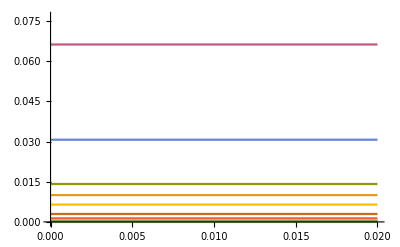

```mathematica
Plot[linear,{x,0,0.02}]
```

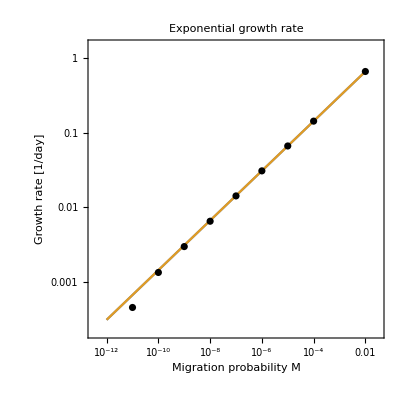

```mathematica
plotSimpleGR=Show[LogLogPlot[{3.07  x^(1/3),3.073 x^(0.3333)},{x,10^-12,10^-2}, Frame->True,FrameLabel->{"Migration probability M","Growth rate [1/day]"}],ListLogLogPlot[linear,PlotStyle->Black], PlotLabel-> "Exponential growth rate",BaseStyle->FontSize->18,AspectRatio->1]
```

```mathematica
Export["/home/s1338295/Documents/Thesis/lattice-models/figures/SimpleGR.eps",plotSimpleGR]
```

/home/s1338295/Documents/Thesis/lattice-models/figures/SimpleGR.eps

```mathematica
dat1={{0,0},{1.*^-7,0.0028171},{1.*^-6,0.007089}}
```

{{0,0},{1.×10^-7,0.0028171},{1.×10^-6,0.007089}}

```mathematica
center=Row[{#,Invisible[#]},""]&;
tickSpecification=Table[{n 10^-7,center@Rotate[ToString[n 0.1]"×10^-6",90 Degree]},{n,Range[0,12]}]
```

{{0,0. ×10^-60. ×10^-6},{1/10000000,0.1 ×10^-60.1 ×10^-6},{1/5000000,0.2 ×10^-60.2 ×10^-6},{3/10000000,0.3 ×10^-60.3 ×10^-6},{1/2500000,0.4 ×10^-60.4 ×10^-6},{1/2000000,0.5 ×10^-60.5 ×10^-6},{3/5000000,0.6 ×10^-60.6 ×10^-6},{7/10000000,0.7 ×10^-60.7 ×10^-6},{1/1250000,0.8 ×10^-60.8 ×10^-6},{9/10000000,0.9 ×10^-60.9 ×10^-6},{1/1000000,1. ×10^-61. ×10^-6},{11/10000000,1.1 ×10^-61.1 ×10^-6},{3/2500000,1.2 ×10^-61.2 ×10^-6}}

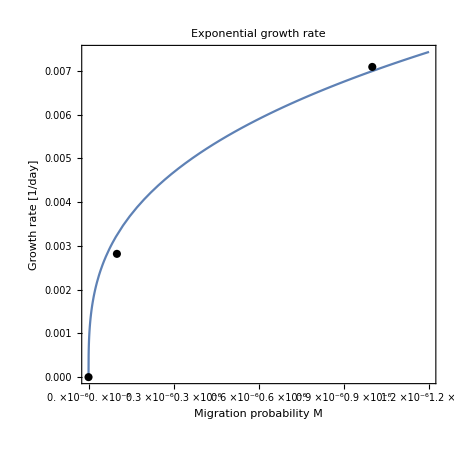

```mathematica
plotLatticeGR=Show[Plot[{0.6994  x^(1/3)},{x,0,1.2 10^-6}, Frame->True,FrameTicks-> {{Automatic,None},{tickSpecification,None}},FrameLabel->{"Migration probability M","Growth rate [1/day]"}],ListPlot[dat1,PlotStyle->Black], PlotLabel-> "Exponential growth rate",BaseStyle->FontSize->18,AspectRatio->1]
```

```mathematica
Export["/home/s1338295/Documents/Thesis/lattice-models/figures/LatticeGR.pdf",plotLatticeGR]
```

/home/s1338295/Documents/Thesis/lattice-models/figures/LatticeGR.pdf